# 600-Cell

### Author

Eric W. Weisstein
June 12, 2019

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polytopes/600-Cell.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/600-Cell.html.

©2019 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

Projection and animation from Russell Towle
Ed Pegg, Jr.

## Sources

[Submitted on 26 Sep 2023]
The Icosidodecahedron
John C. Baez

https://arxiv.org/abs/2309.15774

## Construction

### Vertices

```mathematica
EvenPermutationQ[p_]:=Signature[p]==-1
EvenPermutations[l_List]:=Module[{p=Permutations[Range[Length[l]]]},Permutations[l][[Flatten[Position[p,_?EvenPermutationQ,1,Heads->False]]]]
]
```

```mathematica
pm[n_]:=Flatten[Outer[List,Sequence@@Table[{-1,1},{n}]],n-1]
```

```mathematica
Cell600Construction:=With[{s=√5,r=GoldenRatio},
Module[{
vs={
EvenPermutations[{r#1,#2,#3/r,0}]&@@@pm[3],
Permutations[{2#1,0,0,0}]&@@@pm[1],
{pm[4]}
}
},
Union[Flatten[#,1]]&/@vs
]
]
```

```mathematica
Length/@Cell600Construction
```

{96,8,16}

```mathematica
v=GoldenRatio/2Join@@Cell600Construction
```

{{-GoldenRatio/2,0,-GoldenRatio^2/2,-1/2},{-GoldenRatio/2,0,-GoldenRatio^2/2,1/2},{-GoldenRatio/2,0,GoldenRatio^2/2,-1/2},{-GoldenRatio/2,0,GoldenRatio^2/2,1/2},{-GoldenRatio/2,-1/2,0,-GoldenRatio^2/2},{-GoldenRatio/2,-1/2,0,GoldenRatio^2/2},{-GoldenRatio/2,1/2,0,-GoldenRatio^2/2},{-GoldenRatio/2,1/2,0,GoldenRatio^2/2},{-GoldenRatio/2,-GoldenRatio^2/2,-1/2,0},{-GoldenRatio/2,-GoldenRatio^2/2,1/2,0},{-GoldenRatio/2,GoldenRatio^2/2,-1/2,0},{-GoldenRatio/2,GoldenRatio^2/2,1/2,0},{0,-GoldenRatio/2,-1/2,-GoldenRatio^2/2},{0,-GoldenRatio/2,-1/2,GoldenRatio^2/2},{0,-GoldenRatio/2,1/2,-GoldenRatio^2/2},{0,-GoldenRatio/2,1/2,GoldenRatio^2/2},{0,GoldenRatio/2,-1/2,-GoldenRatio^2/2},{0,GoldenRatio/2,-1/2,GoldenRatio^2/2},{0,GoldenRatio/2,1/2,-GoldenRatio^2/2},{0,GoldenRatio/2,1/2,GoldenRatio^2/2},{0,-1/2,-GoldenRatio^2/2,-GoldenRatio/2},{0,-1/2,-GoldenRatio^2/2,GoldenRatio/2},{0,-1/2,GoldenRatio^2/2,-GoldenRatio/2},{0,-1/2,GoldenRatio^2/2,GoldenRatio/2},{0,1/2,-GoldenRatio^2/2,-GoldenRatio/2},{0,1/2,-GoldenRatio^2/2,GoldenRatio/2},{0,1/2,GoldenRatio^2/2,-GoldenRatio/2},{0,1/2,GoldenRatio^2/2,GoldenRatio/2},{0,-GoldenRatio^2/2,-GoldenRatio/2,-1/2},{0,-GoldenRatio^2/2,-GoldenRatio/2,1/2},{0,-GoldenRatio^2/2,GoldenRatio/2,-1/2},{0,-GoldenRatio^2/2,GoldenRatio/2,1/2},{0,GoldenRatio^2/2,-GoldenRatio/2,-1/2},{0,GoldenRatio^2/2,-GoldenRatio/2,1/2},{0,GoldenRatio^2/2,GoldenRatio/2,-1/2},{0,GoldenRatio^2/2,GoldenRatio/2,1/2},{GoldenRatio/2,0,-GoldenRatio^2/2,-1/2},{GoldenRatio/2,0,-GoldenRatio^2/2,1/2},{GoldenRatio/2,0,GoldenRatio^2/2,-1/2},{GoldenRatio/2,0,GoldenRatio^2/2,1/2},{GoldenRatio/2,-1/2,0,-GoldenRatio^2/2},{GoldenRatio/2,-1/2,0,GoldenRatio^2/2},{GoldenRatio/2,1/2,0,-GoldenRatio^2/2},{GoldenRatio/2,1/2,0,GoldenRatio^2/2},{GoldenRatio/2,-GoldenRatio^2/2,-1/2,0},{GoldenRatio/2,-GoldenRatio^2/2,1/2,0},{GoldenRatio/2,GoldenRatio^2/2,-1/2,0},{GoldenRatio/2,GoldenRatio^2/2,1/2,0},{-1/2,-GoldenRatio/2,-GoldenRatio^2/2,0},{-1/2,-GoldenRatio/2,GoldenRatio^2/2,0},{-1/2,0,-GoldenRatio/2,-GoldenRatio^2/2},{-1/2,0,-GoldenRatio/2,GoldenRatio^2/2},{-1/2,0,GoldenRatio/2,-GoldenRatio^2/2},{-1/2,0,GoldenRatio/2,GoldenRatio^2/2},{-1/2,GoldenRatio/2,-GoldenRatio^2/2,0},{-1/2,GoldenRatio/2,GoldenRatio^2/2,0},{-1/2,-GoldenRatio^2/2,0,-GoldenRatio/2},{-1/2,-GoldenRatio^2/2,0,GoldenRatio/2},{-1/2,GoldenRatio^2/2,0,-GoldenRatio/2},{-1/2,GoldenRatio^2/2,0,GoldenRatio/2},{1/2,-GoldenRatio/2,-GoldenRatio^2/2,0},{1/2,-GoldenRatio/2,GoldenRatio^2/2,0},{1/2,0,-GoldenRatio/2,-GoldenRatio^2/2},{1/2,0,-GoldenRatio/2,GoldenRatio^2/2},{1/2,0,GoldenRatio/2,-GoldenRatio^2/2},{1/2,0,GoldenRatio/2,GoldenRatio^2/2},{1/2,GoldenRatio/2,-GoldenRatio^2/2,0},{1/2,GoldenRatio/2,GoldenRatio^2/2,0},{1/2,-GoldenRatio^2/2,0,-GoldenRatio/2},{1/2,-GoldenRatio^2/2,0,GoldenRatio/2},{1/2,GoldenRatio^2/2,0,-GoldenRatio/2},{1/2,GoldenRatio^2/2,0,GoldenRatio/2},{-GoldenRatio^2/2,-GoldenRatio/2,0,-1/2},{-GoldenRatio^2/2,-GoldenRatio/2,0,1/2},{-GoldenRatio^2/2,0,-1/2,-GoldenRatio/2},{-GoldenRatio^2/2,0,-1/2,GoldenRatio/2},{-GoldenRatio^2/2,0,1/2,-GoldenRatio/2},{-GoldenRatio^2/2,0,1/2,GoldenRatio/2},{-GoldenRatio^2/2,GoldenRatio/2,0,-1/2},{-GoldenRatio^2/2,GoldenRatio/2,0,1/2},{-GoldenRatio^2/2,-1/2,-GoldenRatio/2,0},{-GoldenRatio^2/2,-1/2,GoldenRatio/2,0},{-GoldenRatio^2/2,1/2,-GoldenRatio/2,0},{-GoldenRatio^2/2,1/2,GoldenRatio/2,0},{GoldenRatio^2/2,-GoldenRatio/2,0,-1/2},{GoldenRatio^2/2,-GoldenRatio/2,0,1/2},{GoldenRatio^2/2,0,-1/2,-GoldenRatio/2},{GoldenRatio^2/2,0,-1/2,GoldenRatio/2},{GoldenRatio^2/2,0,1/2,-GoldenRatio/2},{GoldenRatio^2/2,0,1/2,GoldenRatio/2},{GoldenRatio^2/2,GoldenRatio/2,0,-1/2},{GoldenRatio^2/2,GoldenRatio/2,0,1/2},{GoldenRatio^2/2,-1/2,-GoldenRatio/2,0},{GoldenRatio^2/2,-1/2,GoldenRatio/2,0},{GoldenRatio^2/2,1/2,-GoldenRatio/2,0},{GoldenRatio^2/2,1/2,GoldenRatio/2,0},{-GoldenRatio,0,0,0},{0,-GoldenRatio,0,0},{0,0,-GoldenRatio,0},{0,0,0,-GoldenRatio},{0,0,0,GoldenRatio},{0,0,GoldenRatio,0},{0,GoldenRatio,0,0},{GoldenRatio,0,0,0},{-GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2},{-GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2},{-GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2},{-GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2,GoldenRatio/2},{-GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2},{-GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2},{-GoldenRatio/2,GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2},{-GoldenRatio/2,GoldenRatio/2,GoldenRatio/2,GoldenRatio/2},{GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2},{GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2},{GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2},{GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2,GoldenRatio/2},{GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2,-GoldenRatio/2},{GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2,GoldenRatio/2},{GoldenRatio/2,GoldenRatio/2,GoldenRatio/2,-GoldenRatio/2},{GoldenRatio/2,GoldenRatio/2,GoldenRatio/2,GoldenRatio/2}}

### VertexCount

```mathematica
Length[v]
```

120

### Edges

```mathematica
Length[e=Select[Subsets[Range[Length[v]],{2}],EuclideanDistance@@v[[#]]==2/GoldenRatio&]]
```

48

```mathematica
Length[e=Select[Subsets[Range[Length[v]],{2}],N[EuclideanDistance@@v[[#]],20]==1&]]
```

720

```mathematica
e
```

{{1,2},{1,21},{1,25},{1,49},{1,51},{1,55},{1,75},{1,81},{1,83},{1,99},{1,105},{1,109},{2,22},{2,26},{2,49},{2,52},{2,55},{2,76},{2,81},{2,83},{2,99},{2,106},{2,110},{3,4},{3,23},{3,27},{3,50},{3,53},{3,56},{3,77},{3,82},{3,84},{3,102},{3,107},{3,111},{4,24},{4,28},{4,50},{4,54},{4,56},{4,78},{4,82},{4,84},{4,102},{4,108},{4,112},{5,7},{5,13},{5,15},{5,51},{5,53},{5,57},{5,73},{5,75},{5,77},{5,100},{5,105},{5,107},{6,8},{6,14},{6,16},{6,52},{6,54},{6,58},{6,74},{6,76},{6,78},{6,101},{6,106},{6,108},{7,17},{7,19},{7,51},{7,53},{7,59},{7,75},{7,77},{7,79},{7,100},{7,109},{7,111},{8,18},{8,20},{8,52},{8,54},{8,60},{8,76},{8,78},{8,80},{8,101},{8,110},{8,112},{9,10},{9,29},{9,30},{9,49},{9,57},{9,58},{9,73},{9,74},{9,81},{9,98},{9,105},{9,106},{10,31},{10,32},{10,50},{10,57},{10,58},{10,73},{10,74},{10,82},{10,98},{10,107},{10,108},{11,12},{11,33},{11,34},{11,55},{11,59},{11,60},{11,79},{11,80},{11,83},{11,103},{11,109},{11,110},{12,35},{12,36},{12,56},{12,59},{12,60},{12,79},{12,80},{12,84},{12,103},{12,111},{12,112},{13,15},{13,21},{13,29},{13,41},{13,51},{13,57},{13,63},{13,69},{13,100},{13,105},{13,113},{14,16},{14,22},{14,30},{14,42},{14,52},{14,58},{14,64},{14,70},{14,101},{14,106},{14,114},{15,23},{15,31},{15,41},{15,53},{15,57},{15,65},{15,69},{15,100},{15,107},{15,115},{16,24},{16,32},{16,42},{16,54},{16,58},{16,66},{16,70},{16,101},{16,108},{16,116},{17,19},{17,25},{17,33},{17,43},{17,51},{17,59},{17,63},{17,71},{17,100},{17,109},{17,117},{18,20},{18,26},{18,34},{18,44},{18,52},{18,60},{18,64},{18,72},{18,101},{18,110},{18,118},{19,27},{19,35},{19,43},{19,53},{19,59},{19,65},{19,71},{19,100},{19,111},{19,119},{20,28},{20,36},{20,44},{20,54},{20,60},{20,66},{20,72},{20,101},{20,112},{20,120},{21,25},{21,29},{21,37},{21,49},{21,51},{21,61},{21,63},{21,99},{21,105},{21,113},{22,26},{22,30},{22,38},{22,49},{22,52},{22,61},{22,64},{22,99},{22,106},{22,114},{23,27},{23,31},{23,39},{23,50},{23,53},{23,62},{23,65},{23,102},{23,107},{23,115},{24,28},{24,32},{24,40},{24,50},{24,54},{24,62},{24,66},{24,102},{24,108},{24,116},{25,33},{25,37},{25,51},{25,55},{25,63},{25,67},{25,99},{25,109},{25,117},{26,34},{26,38},{26,52},{26,55},{26,64},{26,67},{26,99},{26,110},{26,118},{27,35},{27,39},{27,53},{27,56},{27,65},{27,68},{27,102},{27,111},{27,119},{28,36},{28,40},{28,54},{28,56},{28,66},{28,68},{28,102},{28,112},{28,120},{29,30},{29,45},{29,49},{29,57},{29,61},{29,69},{29,98},{29,105},{29,113},{30,45},{30,49},{30,58},{30,61},{30,70},{30,98},{30,106},{30,114},{31,32},{31,46},{31,50},{31,57},{31,62},{31,69},{31,98},{31,107},{31,115},{32,46},{32,50},{32,58},{32,62},{32,70},{32,98},{32,108},{32,116},{33,34},{33,47},{33,55},{33,59},{33,67},{33,71},{33,103},{33,109},{33,117},{34,47},{34,55},{34,60},{34,67},{34,72},{34,103},{34,110},{34,118},{35,36},{35,48},{35,56},{35,59},{35,68},{35,71},{35,103},{35,111},{35,119},{36,48},{36,56},{36,60},{36,68},{36,72},{36,103},{36,112},{36,120},{37,38},{37,61},{37,63},{37,67},{37,87},{37,93},{37,95},{37,99},{37,113},{37,117},{38,61},{38,64},{38,67},{38,88},{38,93},{38,95},{38,99},{38,114},{38,118},{39,40},{39,62},{39,65},{39,68},{39,89},{39,94},{39,96},{39,102},{39,115},{39,119},{40,62},{40,66},{40,68},{40,90},{40,94},{40,96},{40,102},{40,116},{40,120},{41,43},{41,63},{41,65},{41,69},{41,85},{41,87},{41,89},{41,100},{41,113},{41,115},{42,44},{42,64},{42,66},{42,70},{42,86},{42,88},{42,90},{42,101},{42,114},{42,116},{43,63},{43,65},{43,71},{43,87},{43,89},{43,91},{43,100},{43,117},{43,119},{44,64},{44,66},{44,72},{44,88},{44,90},{44,92},{44,101},{44,118},{44,120},{45,46},{45,61},{45,69},{45,70},{45,85},{45,86},{45,93},{45,98},{45,113},{45,114},{46,62},{46,69},{46,70},{46,85},{46,86},{46,94},{46,98},{46,115},{46,116},{47,48},{47,67},{47,71},{47,72},{47,91},{47,92},{47,95},{47,103},{47,117},{47,118},{48,68},{48,71},{48,72},{48,91},{48,92},{48,96},{48,103},{48,119},{48,120},{49,61},{49,81},{49,99},{49,105},{49,106},{50,62},{50,82},{50,102},{50,107},{50,108},{51,63},{51,75},{51,100},{51,105},{51,109},{52,64},{52,76},{52,101},{52,106},{52,110},{53,65},{53,77},{53,100},{53,107},{53,111},{54,66},{54,78},{54,101},{54,108},{54,112},{55,67},{55,83},{55,99},{55,109},{55,110},{56,68},{56,84},{56,102},{56,111},{56,112},{57,69},{57,73},{57,98},{57,105},{57,107},{58,70},{58,74},{58,98},{58,106},{58,108},{59,71},{59,79},{59,103},{59,109},{59,111},{60,72},{60,80},{60,103},{60,110},{60,112},{61,93},{61,99},{61,113},{61,114},{62,94},{62,102},{62,115},{62,116},{63,87},{63,100},{63,113},{63,117},{64,88},{64,101},{64,114},{64,118},{65,89},{65,100},{65,115},{65,119},{66,90},{66,101},{66,116},{66,120},{67,95},{67,99},{67,117},{67,118},{68,96},{68,102},{68,119},{68,120},{69,85},{69,98},{69,113},{69,115},{70,86},{70,98},{70,114},{70,116},{71,91},{71,103},{71,117},{71,119},{72,92},{72,103},{72,118},{72,120},{73,74},{73,75},{73,77},{73,81},{73,82},{73,97},{73,105},{73,107},{74,76},{74,78},{74,81},{74,82},{74,97},{74,106},{74,108},{75,77},{75,79},{75,81},{75,83},{75,97},{75,105},{75,109},{76,78},{76,80},{76,81},{76,83},{76,97},{76,106},{76,110},{77,79},{77,82},{77,84},{77,97},{77,107},{77,111},{78,80},{78,82},{78,84},{78,97},{78,108},{78,112},{79,80},{79,83},{79,84},{79,97},{79,109},{79,111},{80,83},{80,84},{80,97},{80,110},{80,112},{81,83},{81,97},{81,105},{81,106},{82,84},{82,97},{82,107},{82,108},{83,97},{83,109},{83,110},{84,97},{84,111},{84,112},{85,86},{85,87},{85,89},{85,93},{85,94},{85,104},{85,113},{85,115},{86,88},{86,90},{86,93},{86,94},{86,104},{86,114},{86,116},{87,89},{87,91},{87,93},{87,95},{87,104},{87,113},{87,117},{88,90},{88,92},{88,93},{88,95},{88,104},{88,114},{88,118},{89,91},{89,94},{89,96},{89,104},{89,115},{89,119},{90,92},{90,94},{90,96},{90,104},{90,116},{90,120},{91,92},{91,95},{91,96},{91,104},{91,117},{91,119},{92,95},{92,96},{92,104},{92,118},{92,120},{93,95},{93,104},{93,113},{93,114},{94,96},{94,104},{94,115},{94,116},{95,104},{95,117},{95,118},{96,104},{96,119},{96,120}}

### EdgeLengths

```mathematica
d=Union[EuclideanDistance@@v[[#]]&/@e]//FullSimplify//FunctionExpand//FullSimplify//Union
```

{1}

### Circumradius

```mathematica
Max[FullSimplify[Norm/@v]]
```

1/2 (1+√5)

### Content

```mathematica
ConvexHullMesh[v]
```

```mathematica
RegionMeasure[%]
```

### Faces

```mathematica
faces=Sort[FindCycle[Graph[Range[120],UndirectedEdge@@@e],{3},All][[All,All,1]]]
```

{{1,2,55},{1,21,25},{1,21,51},{1,25,51},{1,25,55},{1,25,109},{1,49,2},{1,49,21},{1,49,81},{1,49,99},{1,51,109},{1,75,51},{1,75,81},{1,75,83},{1,75,109},{1,81,2},{1,83,2},{1,83,55},{1,83,81},{1,83,109},{1,99,2},{1,99,21},{1,99,25},{1,99,55},{1,105,21},{1,105,49},{1,105,51},{1,105,75},{1,105,81},{1,109,55},{2,26,22},{2,26,52},{2,26,55},{2,49,22},{2,52,22},{2,52,76},{2,52,106},{2,55,83},{2,81,49},{2,81,76},{2,81,83},{2,83,76},{2,99,22},{2,99,26},{2,99,49},{2,99,55},{2,106,22},{2,106,49},{2,106,76},{2,110,52},{2,110,55},{2,110,76},{2,110,83},{3,4,50},{3,4,56},{3,23,50},{3,23,107},{3,27,23},{3,27,53},{3,27,56},{3,27,111},{3,53,23},{3,53,107},{3,53,111},{3,56,84},{3,56,111},{3,77,53},{3,77,82},{3,77,107},{3,77,111},{3,82,4},{3,82,50},{3,82,84},{3,82,107},{3,102,4},{3,102,23},{3,102,50},{3,102,56},{3,107,50},{3,111,84},{4,28,56},{4,50,24},{4,54,24},{4,54,28},{4,54,78},{4,82,50},{4,82,78},{4,102,24},{4,102,28},{4,102,50},{4,102,56},{4,108,24},{4,108,50},{4,108,54},{4,108,78},{4,108,82},{4,112,28},{4,112,54},{4,112,56},{4,112,78},{5,7,77},{5,15,13},{5,15,53},{5,15,57},{5,15,107},{5,51,13},{5,53,77},{5,53,107},{5,57,73},{5,57,107},{5,75,51},{5,75,73},{5,75,77},{5,75,105},{5,77,73},{5,100,15},{5,100,51},{5,105,13},{5,105,51},{5,105,57},{5,107,73},{5,107,77},{6,14,101},{6,52,101},{6,54,101},{6,54,108},{6,58,108},{6,74,108},{6,76,52},{6,76,74},{6,78,108},{6,106,74},{6,106,76},{7,5,53},{7,19,53},{7,19,111},{7,51,5},{7,53,111},{7,59,111},{7,75,5},{7,75,77},{7,75,79},{7,77,53},{7,77,111},{7,79,77},{7,79,111},{7,100,5},{7,100,53},{7,109,17},{7,109,75},{7,109,79},{8,6,52},{8,18,52},{8,20,60},{8,20,101},{8,20,112},{8,54,6},{8,54,20},{8,54,78},{8,54,101},{8,54,112},{8,60,18},{8,76,6},{8,76,52},{8,78,6},{8,78,76},{8,78,80},{8,78,112},{8,80,60},{8,80,76},{8,101,6},{8,101,52},{8,110,52},{8,110,60},{8,110,76},{8,110,80},{8,112,60},{8,112,80},{9,10,58},{9,29,30},{9,29,49},{9,29,105},{9,30,49},{9,30,58},{9,30,106},{9,57,10},{9,57,73},{9,73,10},{9,74,10},{9,74,58},{9,74,73},{9,74,81},{9,74,106},{9,81,49},{9,98,10},{9,98,30},{9,98,58},{9,105,81},{9,106,49},{9,106,58},{10,31,50},{10,31,98},{10,32,31},{10,32,50},{10,32,58},{10,32,98},{10,32,108},{10,57,31},{10,57,73},{10,57,98},{10,73,74},{10,73,82},{10,73,107},{10,74,58},{10,82,74},{10,82,107},{10,82,108},{10,98,58},{10,107,31},{10,107,50},{10,108,50},{10,108,58},{10,108,74},{11,12,59},{11,12,79},{11,12,80},{11,33,55},{11,33,59},{11,33,109},{11,34,33},{11,34,55},{11,34,103},{11,34,110},{11,59,109},{11,60,110},{11,79,59},{11,79,80},{11,79,83},{11,79,109},{11,80,83},{11,80,110},{11,83,55},{11,83,109},{11,83,110},{11,103,12},{11,103,33},{11,103,59},{11,109,55},{11,110,55},{12,35,56},{12,35,59},{12,36,56},{12,79,59},{12,79,80},{12,103,59},{12,111,35},{12,111,56},{12,111,59},{12,112,56},{12,112,80},{13,5,100},{13,15,69},{13,15,100},{13,29,21},{13,29,69},{13,29,113},{13,41,15},{13,41,100},{13,51,21},{13,51,100},{13,51,105},{13,63,113},{13,69,113},{13,105,21},{13,105,29},{14,6,52},{14,6,58},{14,22,106},{14,22,114},{14,30,58},{14,30,70},{14,30,106},{14,30,114},{14,70,42},{14,70,58},{14,70,114},{14,101,42},{14,101,52},{14,106,6},{14,106,52},{14,106,58},{15,31,107},{15,31,115},{15,41,65},{15,41,100},{15,41,115},{15,53,107},{15,65,115},{15,69,115},{15,100,65},{16,6,14},{16,24,32},{16,24,54},{16,24,66},{16,24,116},{16,42,14},{16,42,66},{16,54,6},{16,54,66},{16,54,101},{16,58,6},{16,58,14},{16,58,32},{16,70,14},{16,70,32},{16,70,42},{16,70,58},{16,70,116},{16,101,6},{16,101,14},{16,101,42},{16,101,66},{16,108,32},{16,116,32},{16,116,42},{16,116,66},{17,7,100},{17,19,43},{17,19,100},{17,25,33},{17,25,51},{17,25,63},{17,43,100},{17,51,100},{17,59,33},{17,63,51},{17,63,100},{17,71,33},{17,71,43},{17,71,117},{17,109,33},{17,109,51},{17,117,33},{17,117,43},{17,117,63},{18,8,101},{18,8,110},{18,26,52},{18,26,64},{18,26,110},{18,44,64},{18,44,101},{18,52,101},{18,52,110},{18,60,110},{18,64,101},{18,72,34},{18,72,44},{18,72,60},{18,72,118},{18,110,34},{18,118,26},{18,118,34},{18,118,44},{18,118,64},{19,7,59},{19,17,7},{19,17,59},{19,27,35},{19,27,53},{19,43,100},{19,43,119},{19,59,35},{19,65,43},{19,65,53},{19,65,100},{19,65,119},{19,71,35},{19,100,7},{19,100,53},{19,111,27},{19,111,35},{19,111,53},{19,111,59},{19,119,35},{20,8,18},{20,28,36},{20,28,54},{20,36,72},{20,44,18},{20,44,72},{20,54,112},{20,60,18},{20,60,72},{20,72,18},{20,101,18},{20,112,36},{20,120,36},{20,120,72},{21,13,113},{21,29,61},{21,29,113},{21,37,61},{21,37,113},{21,49,29},{21,49,61},{21,61,113},{21,63,37},{21,63,51},{21,63,113},{21,99,61},{21,105,29},{21,105,51},{22,14,52},{22,26,52},{22,26,64},{22,30,106},{22,49,106},{22,61,49},{22,61,99},{22,64,38},{22,99,26},{22,106,52},{22,114,38},{22,114,64},{23,15,65},{23,27,65},{23,39,65},{23,50,102},{23,53,15},{23,53,65},{23,53,107},{23,62,50},{23,62,102},{23,62,115},{23,107,15},{23,107,50},{23,115,15},{23,115,65},{24,4,28},{24,32,116},{24,40,28},{24,50,32},{24,50,62},{24,54,28},{24,62,116},{24,66,28},{24,102,28},{24,102,50},{24,102,62},{25,17,109},{25,17,117},{25,21,37},{25,33,109},{25,33,117},{25,37,117},{25,51,21},{25,51,109},{25,55,33},{25,55,109},{25,63,21},{25,63,37},{25,63,117},{25,67,33},{25,67,37},{25,67,117},{25,99,55},{26,2,110},{26,18,34},{26,22,38},{26,55,34},{26,64,38},{26,67,34},{26,67,38},{26,67,118},{26,99,38},{26,110,34},{26,110,52},{26,118,34},{26,118,38},{27,3,102},{27,19,65},{27,19,119},{27,23,39},{27,23,102},{27,35,56},{27,35,68},{27,35,119},{27,53,23},{27,53,65},{27,53,111},{27,56,68},{27,56,102},{27,65,39},{27,65,119},{27,68,39},{27,68,102},{27,102,39},{27,111,35},{27,111,56},{27,119,39},{27,119,68},{28,20,112},{28,20,120},{28,36,68},{28,36,112},{28,36,120},{28,40,68},{28,40,120},{28,54,112},{28,56,36},{28,56,68},{28,56,112},{28,66,120},{28,68,120},{28,102,56},{28,102,68},{29,9,57},{29,9,98},{29,30,45},{29,30,98},{29,45,98},{29,61,45},{29,61,49},{29,61,113},{29,69,57},{29,69,98},{29,98,57},{29,105,57},{29,113,45},{29,113,69},{30,22,14},{30,22,49},{30,22,61},{30,22,114},{30,49,29},{30,61,29},{30,61,45},{30,61,49},{30,70,45},{30,70,58},{30,70,98},{30,70,114},{30,98,45},{30,106,58},{30,114,45},{31,15,23},{31,15,69},{31,46,62},{31,46,115},{31,50,23},{31,50,62},{31,62,23},{31,98,69},{31,107,23},{31,115,23},{31,115,62},{31,115,69},{32,24,62},{32,31,46},{32,31,62},{32,31,98},{32,46,62},{32,50,62},{32,50,108},{32,70,46},{32,70,58},{32,70,98},{32,98,46},{32,116,46},{32,116,62},{33,47,117},{33,67,117},{33,71,47},{33,71,59},{33,71,117},{33,103,47},{33,103,59},{33,103,71},{33,109,59},{34,33,47},{34,33,55},{34,33,67},{34,67,55},{34,103,33},{34,103,47},{34,118,47},{34,118,67},{35,12,103},{35,36,103},{35,48,68},{35,48,103},{35,48,119},{35,56,68},{35,59,103},{35,71,48},{35,71,103},{35,71,119},{35,119,68},{36,35,12},{36,35,48},{36,35,68},{36,56,68},{36,68,48},{36,103,12},{36,103,48},{36,112,12},{36,120,48},{36,120,68},{37,21,99},{37,25,99},{37,38,95},{37,38,99},{37,61,93},{37,61,99},{37,63,87},{37,63,117},{37,67,95},{37,67,99},{37,67,117},{37,87,93},{37,87,95},{37,93,95},{37,113,61},{37,113,63},{37,113,87},{37,117,87},{37,117,95},{38,22,61},{38,22,99},{38,37,61},{38,64,114},{38,67,37},{38,67,99},{38,88,114},{38,93,37},{38,93,61},{38,93,114},{38,95,67},{38,99,61},{38,114,61},{38,118,67},{39,23,115},{39,62,115},{39,65,115},{39,68,40},{39,68,119},{39,89,96},{39,89,115},{39,89,119},{39,94,40},{39,94,89},{39,94,96},{39,94,115},{39,96,40},{39,102,23},{39,102,40},{39,119,96},{40,62,24},{40,62,94},{40,66,24},{40,66,28},{40,66,90},{40,94,90},{40,96,90},{40,96,94},{40,102,24},{40,102,28},{40,102,62},{40,116,24},{40,116,62},{40,116,90},{40,116,94},{40,120,68},{40,120,90},{40,120,96},{41,13,69},{41,13,113},{41,15,69},{41,43,89},{41,63,113},{41,65,115},{41,69,113},{41,85,69},{41,85,87},{41,85,89},{41,85,113},{41,87,89},{41,87,113},{41,115,69},{41,115,85},{41,115,89},{42,14,114},{42,44,90},{42,64,101},{42,64,114},{42,66,90},{42,70,86},{42,70,114},{42,86,88},{42,86,90},{42,86,114},{42,88,64},{42,88,90},{42,88,114},{42,116,66},{42,116,70},{42,116,86},{42,116,90},{43,17,63},{43,65,41},{43,71,117},{43,87,41},{43,87,63},{43,87,89},{43,87,117},{43,91,89},{43,91,117},{43,91,119},{43,100,41},{43,100,63},{43,117,63},{43,119,89},{44,20,66},{44,42,66},{44,64,42},{44,64,88},{44,64,118},{44,88,42},{44,88,90},{44,88,92},{44,88,118},{44,90,66},{44,92,90},{44,92,118},{44,92,120},{44,101,42},{44,101,66},{44,120,20},{44,120,66},{44,120,90},{45,29,69},{45,46,85},{45,46,86},{45,61,93},{45,61,113},{45,70,46},{45,70,86},{45,70,114},{45,85,69},{45,85,93},{45,86,85},{45,86,93},{45,98,69},{45,113,69},{45,113,85},{45,114,86},{46,31,69},{46,45,69},{46,62,94},{46,62,116},{46,70,116},{46,85,69},{46,86,116},{46,94,85},{46,94,116},{46,98,69},{46,115,69},{46,115,85},{47,33,67},{47,34,67},{47,48,92},{47,71,103},{47,71,117},{47,95,67},{47,95,92},{47,95,117},{47,95,118},{47,117,67},{47,118,67},{47,118,92},{48,71,47},{48,71,91},{48,71,119},{48,91,119},{48,96,91},{48,96,119},{48,103,47},{48,120,96},{49,9,105},{49,21,105},{49,22,99},{49,29,105},{49,30,106},{49,61,99},{49,81,105},{50,31,107},{50,32,31},{50,62,102},{51,17,7},{51,63,25},{51,63,100},{51,75,7},{51,100,7},{51,109,7},{52,6,106},{52,14,64},{52,18,64},{52,22,64},{52,26,64},{52,76,106},{52,101,64},{53,5,100},{53,15,65},{53,15,100},{53,65,100},{53,107,77},{53,111,77},{54,20,101},{54,78,6},{54,78,108},{54,112,78},{55,25,67},{55,26,67},{55,33,67},{55,33,109},{55,83,109},{55,99,26},{55,99,67},{56,36,35},{56,36,112},{56,111,35},{57,5,13},{57,10,107},{57,15,13},{57,15,31},{57,15,69},{57,15,107},{57,29,13},{57,69,13},{57,69,31},{57,73,107},{57,98,9},{57,98,31},{57,98,69},{57,105,9},{57,105,13},{57,107,31},{58,6,74},{58,30,98},{58,32,98},{58,32,108},{58,70,98},{58,74,108},{58,106,6},{58,106,74},{59,17,7},{59,17,71},{59,35,71},{59,79,7},{59,103,71},{60,11,12},{60,11,34},{60,11,80},{60,18,34},{60,36,12},{60,36,20},{60,72,34},{60,72,103},{60,80,12},{60,80,110},{60,80,112},{60,103,11},{60,103,12},{60,103,34},{60,103,36},{60,110,34},{60,112,12},{60,112,20},{60,112,36},{61,22,114},{61,30,114},{61,45,114},{61,93,114},{62,23,39},{62,40,39},{62,46,115},{62,94,39},{62,94,116},{62,102,39},{63,13,41},{63,21,13},{63,43,41},{63,51,13},{63,87,41},{63,87,117},{63,100,13},{63,100,41},{63,113,87},{64,22,14},{64,42,14},{64,88,38},{64,88,114},{64,88,118},{64,101,14},{64,114,14},{64,118,26},{64,118,38},{65,41,89},{65,41,100},{65,43,89},{65,43,100},{65,43,119},{65,89,39},{65,115,89},{65,119,39},{65,119,89},{66,20,28},{66,20,54},{66,20,101},{66,20,120},{66,28,54},{66,40,116},{66,40,120},{66,42,101},{66,54,24},{66,54,101},{66,116,24},{66,116,90},{66,120,90},{67,26,99},{67,99,25},{67,117,95},{67,118,95},{68,119,48},{68,120,48},{69,85,113},{69,115,85},{70,46,86},{70,86,116},{70,114,86},{70,116,32},{71,17,19},{71,43,19},{71,43,91},{71,43,119},{71,59,19},{71,91,119},{71,103,48},{71,117,91},{71,119,19},{72,34,47},{72,34,118},{72,36,120},{72,44,120},{72,48,36},{72,48,47},{72,48,120},{72,60,36},{72,92,44},{72,92,47},{72,92,48},{72,92,118},{72,92,120},{72,103,34},{72,103,36},{72,103,47},{72,103,48},{72,118,44},{72,118,47},{73,5,105},{73,9,81},{73,9,105},{73,57,105},{73,74,81},{73,74,97},{73,75,81},{73,75,97},{73,75,105},{73,77,97},{73,77,107},{73,82,97},{73,82,107},{73,97,81},{73,105,81},{74,73,82},{74,76,106},{74,81,76},{74,97,76},{74,97,81},{74,97,82},{75,51,105},{75,73,77},{75,79,77},{75,79,109},{75,97,77},{75,97,79},{75,105,81},{75,109,51},{76,6,78},{76,52,110},{76,80,78},{76,80,110},{76,97,78},{77,3,84},{77,79,84},{77,79,97},{77,82,84},{77,82,107},{77,111,84},{78,6,74},{78,76,74},{78,80,112},{78,97,74},{78,108,74},{79,12,111},{79,59,111},{79,77,111},{79,83,109},{80,76,83},{80,76,97},{80,78,97},{80,79,83},{80,79,97},{80,83,97},{81,2,106},{81,9,106},{81,49,106},{81,74,106},{81,75,97},{81,76,97},{81,76,106},{81,83,97},{82,10,50},{82,74,78},{82,74,108},{82,77,73},{82,77,97},{82,97,78},{82,107,50},{82,108,50},{82,108,78},{83,75,81},{83,76,81},{83,79,75},{83,97,75},{83,109,75},{84,3,4},{84,56,4},{84,56,12},{84,77,97},{84,78,4},{84,78,80},{84,78,82},{84,78,97},{84,79,12},{84,79,80},{84,79,97},{84,79,111},{84,80,12},{84,80,97},{84,82,4},{84,82,97},{84,111,12},{84,111,56},{84,112,4},{84,112,12},{84,112,56},{84,112,78},{84,112,80},{85,86,94},{85,87,89},{85,87,113},{85,93,86},{85,94,89},{85,104,86},{85,104,89},{85,104,94},{85,115,89},{86,85,46},{86,90,88},{86,90,104},{86,90,116},{86,93,88},{86,94,46},{86,94,104},{86,104,88},{86,114,88},{87,91,43},{87,93,85},{87,93,104},{87,104,85},{87,117,91},{88,90,104},{88,92,95},{88,92,118},{88,95,38},{88,104,95},{88,118,38},{88,118,95},{89,87,104},{89,91,87},{89,91,96},{89,91,119},{89,94,96},{89,104,94},{89,104,96},{90,86,94},{90,96,94},{90,96,120},{90,104,94},{90,116,94},{91,48,47},{91,71,47},{91,87,104},{91,89,104},{91,92,47},{91,95,47},{91,95,92},{91,95,104},{91,96,92},{91,104,92},{91,117,47},{92,90,88},{92,91,48},{92,95,118},{92,96,48},{92,96,90},{92,104,88},{92,104,90},{92,120,48},{92,120,90},{92,120,96},{93,37,113},{93,38,88},{93,45,113},{93,45,114},{93,61,113},{93,85,113},{93,86,114},{93,87,113},{93,104,85},{93,104,86},{93,104,88},{93,114,88},{94,46,115},{94,62,115},{94,85,115},{94,86,116},{94,89,115},{95,38,93},{95,87,93},{95,88,93},{95,91,87},{95,92,104},{95,104,87},{95,104,93},{95,117,87},{95,117,91},{95,118,38},{96,39,68},{96,40,68},{96,48,68},{96,89,119},{96,91,119},{96,104,91},{96,119,68},{96,120,68},{97,76,83},{97,79,83},{98,31,46},{98,45,46},{98,70,45},{98,70,46},{99,25,21},{99,49,21},{101,20,44},{101,64,44},{102,39,68},{102,68,40},{102,68,56},{104,90,96},{104,94,96},{104,96,92},{108,6,16},{108,24,16},{108,32,24},{108,50,24},{108,54,16},{108,54,24},{108,58,16},{109,7,59},{109,17,59},{109,79,59},{110,26,55},{110,34,55},{110,55,83},{110,76,83},{110,80,83},{111,35,59}}

```mathematica
Length[faces]
```

1200

### Cells

```mathematica
Length[v]
```

120

Vertices adjacent to i for each i

```mathematica
indexed=Table[{i,Flatten@DeleteCases[Select[e,!FreeQ[#,i]&],i,{2}]},{i,120}]
```

{{1,{2,21,25,49,51,55,75,81,83,99,105,109}},{2,{1,22,26,49,52,55,76,81,83,99,106,110}},{3,{4,23,27,50,53,56,77,82,84,102,107,111}},{4,{3,24,28,50,54,56,78,82,84,102,108,112}},{5,{7,13,15,51,53,57,73,75,77,100,105,107}},{6,{8,14,16,52,54,58,74,76,78,101,106,108}},{7,{5,17,19,51,53,59,75,77,79,100,109,111}},{8,{6,18,20,52,54,60,76,78,80,101,110,112}},{9,{10,29,30,49,57,58,73,74,81,98,105,106}},{10,{9,31,32,50,57,58,73,74,82,98,107,108}},{11,{12,33,34,55,59,60,79,80,83,103,109,110}},{12,{11,35,36,56,59,60,79,80,84,103,111,112}},{13,{5,15,21,29,41,51,57,63,69,100,105,113}},{14,{6,16,22,30,42,52,58,64,70,101,106,114}},{15,{5,13,23,31,41,53,57,65,69,100,107,115}},{16,{6,14,24,32,42,54,58,66,70,101,108,116}},{17,{7,19,25,33,43,51,59,63,71,100,109,117}},{18,{8,20,26,34,44,52,60,64,72,101,110,118}},{19,{7,17,27,35,43,53,59,65,71,100,111,119}},{20,{8,18,28,36,44,54,60,66,72,101,112,120}},{21,{1,13,25,29,37,49,51,61,63,99,105,113}},{22,{2,14,26,30,38,49,52,61,64,99,106,114}},{23,{3,15,27,31,39,50,53,62,65,102,107,115}},{24,{4,16,28,32,40,50,54,62,66,102,108,116}},{25,{1,17,21,33,37,51,55,63,67,99,109,117}},{26,{2,18,22,34,38,52,55,64,67,99,110,118}},{27,{3,19,23,35,39,53,56,65,68,102,111,119}},{28,{4,20,24,36,40,54,56,66,68,102,112,120}},{29,{9,13,21,30,45,49,57,61,69,98,105,113}},{30,{9,14,22,29,45,49,58,61,70,98,106,114}},{31,{10,15,23,32,46,50,57,62,69,98,107,115}},{32,{10,16,24,31,46,50,58,62,70,98,108,116}},{33,{11,17,25,34,47,55,59,67,71,103,109,117}},{34,{11,18,26,33,47,55,60,67,72,103,110,118}},{35,{12,19,27,36,48,56,59,68,71,103,111,119}},{36,{12,20,28,35,48,56,60,68,72,103,112,120}},{37,{21,25,38,61,63,67,87,93,95,99,113,117}},{38,{22,26,37,61,64,67,88,93,95,99,114,118}},{39,{23,27,40,62,65,68,89,94,96,102,115,119}},{40,{24,28,39,62,66,68,90,94,96,102,116,120}},{41,{13,15,43,63,65,69,85,87,89,100,113,115}},{42,{14,16,44,64,66,70,86,88,90,101,114,116}},{43,{17,19,41,63,65,71,87,89,91,100,117,119}},{44,{18,20,42,64,66,72,88,90,92,101,118,120}},{45,{29,30,46,61,69,70,85,86,93,98,113,114}},{46,{31,32,45,62,69,70,85,86,94,98,115,116}},{47,{33,34,48,67,71,72,91,92,95,103,117,118}},{48,{35,36,47,68,71,72,91,92,96,103,119,120}},{49,{1,2,9,21,22,29,30,61,81,99,105,106}},{50,{3,4,10,23,24,31,32,62,82,102,107,108}},{51,{1,5,7,13,17,21,25,63,75,100,105,109}},{52,{2,6,8,14,18,22,26,64,76,101,106,110}},{53,{3,5,7,15,19,23,27,65,77,100,107,111}},{54,{4,6,8,16,20,24,28,66,78,101,108,112}},{55,{1,2,11,25,26,33,34,67,83,99,109,110}},{56,{3,4,12,27,28,35,36,68,84,102,111,112}},{57,{5,9,10,13,15,29,31,69,73,98,105,107}},{58,{6,9,10,14,16,30,32,70,74,98,106,108}},{59,{7,11,12,17,19,33,35,71,79,103,109,111}},{60,{8,11,12,18,20,34,36,72,80,103,110,112}},{61,{21,22,29,30,37,38,45,49,93,99,113,114}},{62,{23,24,31,32,39,40,46,50,94,102,115,116}},{63,{13,17,21,25,37,41,43,51,87,100,113,117}},{64,{14,18,22,26,38,42,44,52,88,101,114,118}},{65,{15,19,23,27,39,41,43,53,89,100,115,119}},{66,{16,20,24,28,40,42,44,54,90,101,116,120}},{67,{25,26,33,34,37,38,47,55,95,99,117,118}},{68,{27,28,35,36,39,40,48,56,96,102,119,120}},{69,{13,15,29,31,41,45,46,57,85,98,113,115}},{70,{14,16,30,32,42,45,46,58,86,98,114,116}},{71,{17,19,33,35,43,47,48,59,91,103,117,119}},{72,{18,20,34,36,44,47,48,60,92,103,118,120}},{73,{5,9,10,57,74,75,77,81,82,97,105,107}},{74,{6,9,10,58,73,76,78,81,82,97,106,108}},{75,{1,5,7,51,73,77,79,81,83,97,105,109}},{76,{2,6,8,52,74,78,80,81,83,97,106,110}},{77,{3,5,7,53,73,75,79,82,84,97,107,111}},{78,{4,6,8,54,74,76,80,82,84,97,108,112}},{79,{7,11,12,59,75,77,80,83,84,97,109,111}},{80,{8,11,12,60,76,78,79,83,84,97,110,112}},{81,{1,2,9,49,73,74,75,76,83,97,105,106}},{82,{3,4,10,50,73,74,77,78,84,97,107,108}},{83,{1,2,11,55,75,76,79,80,81,97,109,110}},{84,{3,4,12,56,77,78,79,80,82,97,111,112}},{85,{41,45,46,69,86,87,89,93,94,104,113,115}},{86,{42,45,46,70,85,88,90,93,94,104,114,116}},{87,{37,41,43,63,85,89,91,93,95,104,113,117}},{88,{38,42,44,64,86,90,92,93,95,104,114,118}},{89,{39,41,43,65,85,87,91,94,96,104,115,119}},{90,{40,42,44,66,86,88,92,94,96,104,116,120}},{91,{43,47,48,71,87,89,92,95,96,104,117,119}},{92,{44,47,48,72,88,90,91,95,96,104,118,120}},{93,{37,38,45,61,85,86,87,88,95,104,113,114}},{94,{39,40,46,62,85,86,89,90,96,104,115,116}},{95,{37,38,47,67,87,88,91,92,93,104,117,118}},{96,{39,40,48,68,89,90,91,92,94,104,119,120}},{97,{73,74,75,76,77,78,79,80,81,82,83,84}},{98,{9,10,29,30,31,32,45,46,57,58,69,70}},{99,{1,2,21,22,25,26,37,38,49,55,61,67}},{100,{5,7,13,15,17,19,41,43,51,53,63,65}},{101,{6,8,14,16,18,20,42,44,52,54,64,66}},{102,{3,4,23,24,27,28,39,40,50,56,62,68}},{103,{11,12,33,34,35,36,47,48,59,60,71,72}},{104,{85,86,87,88,89,90,91,92,93,94,95,96}},{105,{1,5,9,13,21,29,49,51,57,73,75,81}},{106,{2,6,9,14,22,30,49,52,58,74,76,81}},{107,{3,5,10,15,23,31,50,53,57,73,77,82}},{108,{4,6,10,16,24,32,50,54,58,74,78,82}},{109,{1,7,11,17,25,33,51,55,59,75,79,83}},{110,{2,8,11,18,26,34,52,55,60,76,80,83}},{111,{3,7,12,19,27,35,53,56,59,77,79,84}},{112,{4,8,12,20,28,36,54,56,60,78,80,84}},{113,{13,21,29,37,41,45,61,63,69,85,87,93}},{114,{14,22,30,38,42,45,61,64,70,86,88,93}},{115,{15,23,31,39,41,46,62,65,69,85,89,94}},{116,{16,24,32,40,42,46,62,66,70,86,90,94}},{117,{17,25,33,37,43,47,63,67,71,87,91,95}},{118,{18,26,34,38,44,47,64,67,72,88,92,95}},{119,{19,27,35,39,43,48,65,68,71,89,91,96}},{120,{20,28,36,40,44,48,66,68,72,90,92,96}}}

Pick the 3-subsets of adjacenct vertices such that all correspond to edges:

```mathematica
data={#[[1]],Select[Subsets[#[[2]],{3}],Length[Intersection[Sort/@Subsets[#,{2}],e]]==3&]}&/@indexed
```

{{1,{{2,49,81},{2,49,99},{2,55,83},{2,55,99},{2,81,83},{21,25,51},{21,25,99},{21,49,99},{21,49,105},{21,51,105},{25,51,109},{25,55,99},{25,55,109},{49,81,105},{51,75,105},{51,75,109},{55,83,109},{75,81,83},{75,81,105},{75,83,109}}},118,{120,{{20,28,36},{20,28,66},17,{90,92,96}}}}
 |  |  |  |

Add back i, sort, and union to get the tetrahedral cells:

```mathematica
Union[Sort/@Flatten[Function[{i,l},Prepend[#,i]&/@l]@@@data,1]]
```

{{1,2,49,81},{1,2,49,99},{1,2,55,83},{1,2,55,99},{1,2,81,83},{1,21,25,51},{1,21,25,99},{1,21,49,99},{1,21,49,105},{1,21,51,105},{1,25,51,109},{1,25,55,99},{1,25,55,109},{1,49,81,105},{1,51,75,105},{1,51,75,109},{1,55,83,109},{1,75,81,83},{1,75,81,105},{1,75,83,109},{2,22,26,52},{2,22,26,99},{2,22,49,99},{2,22,49,106},{2,22,52,106},{2,26,52,110},{2,26,55,99},{2,26,55,110},{2,49,81,106},{2,52,76,106},{2,52,76,110},{2,55,83,110},{2,76,81,83},{2,76,81,106},{2,76,83,110},{3,4,50,82},{3,4,50,102},{3,4,56,84},{3,4,56,102},{3,4,82,84},{3,23,27,53},{3,23,27,102},{3,23,50,102},{3,23,50,107},{3,23,53,107},{3,27,53,111},{3,27,56,102},{3,27,56,111},{3,50,82,107},{3,53,77,107},{3,53,77,111},{3,56,84,111},{3,77,82,84},{3,77,82,107},{3,77,84,111},{4,24,28,54},{4,24,28,102},{4,24,50,102},{4,24,50,108},{4,24,54,108},{4,28,54,112},{4,28,56,102},{4,28,56,112},{4,50,82,108},{4,54,78,108},{4,54,78,112},{4,56,84,112},{4,78,82,84},{4,78,82,108},{4,78,84,112},{5,7,51,75},{5,7,51,100},{5,7,53,77},{5,7,53,100},{5,7,75,77},{5,13,15,57},{5,13,15,100},{5,13,51,100},{5,13,51,105},{5,13,57,105},{5,15,53,100},{5,15,53,107},{5,15,57,107},{5,51,75,105},{5,53,77,107},{5,57,73,105},{5,57,73,107},{5,73,75,77},{5,73,75,105},{5,73,77,107},{6,8,52,76},{6,8,52,101},{6,8,54,78},{6,8,54,101},{6,8,76,78},{6,14,16,58},{6,14,16,101},{6,14,52,101},{6,14,52,106},{6,14,58,106},{6,16,54,101},{6,16,54,108},{6,16,58,108},{6,52,76,106},{6,54,78,108},{6,58,74,106},{6,58,74,108},{6,74,76,78},{6,74,76,106},{6,74,78,108},{7,17,19,59},{7,17,19,100},{7,17,51,100},{7,17,51,109},{7,17,59,109},{7,19,53,100},{7,19,53,111},{7,19,59,111},{7,51,75,109},{7,53,77,111},{7,59,79,109},{7,59,79,111},{7,75,77,79},{7,75,79,109},{7,77,79,111},{8,18,20,60},{8,18,20,101},{8,18,52,101},{8,18,52,110},{8,18,60,110},{8,20,54,101},{8,20,54,112},{8,20,60,112},{8,52,76,110},{8,54,78,112},{8,60,80,110},{8,60,80,112},{8,76,78,80},{8,76,80,110},{8,78,80,112},{9,10,57,73},{9,10,57,98},{9,10,58,74},{9,10,58,98},{9,10,73,74},{9,29,30,49},{9,29,30,98},{9,29,49,105},{9,29,57,98},{9,29,57,105},{9,30,49,106},{9,30,58,98},{9,30,58,106},{9,49,81,105},{9,49,81,106},{9,57,73,105},{9,58,74,106},{9,73,74,81},{9,73,81,105},{9,74,81,106},{10,31,32,50},{10,31,32,98},{10,31,50,107},{10,31,57,98},{10,31,57,107},{10,32,50,108},{10,32,58,98},{10,32,58,108},{10,50,82,107},{10,50,82,108},{10,57,73,107},{10,58,74,108},{10,73,74,82},{10,73,82,107},{10,74,82,108},{11,12,59,79},{11,12,59,103},{11,12,60,80},{11,12,60,103},{11,12,79,80},{11,33,34,55},{11,33,34,103},{11,33,55,109},{11,33,59,103},{11,33,59,109},{11,34,55,110},{11,34,60,103},{11,34,60,110},{11,55,83,109},{11,55,83,110},{11,59,79,109},{11,60,80,110},{11,79,80,83},{11,79,83,109},{11,80,83,110},{12,35,36,56},{12,35,36,103},{12,35,56,111},{12,35,59,103},{12,35,59,111},{12,36,56,112},{12,36,60,103},{12,36,60,112},{12,56,84,111},{12,56,84,112},{12,59,79,111},{12,60,80,112},{12,79,80,84},{12,79,84,111},{12,80,84,112},{13,15,41,69},{13,15,41,100},{13,15,57,69},{13,21,29,105},{13,21,29,113},{13,21,51,63},{13,21,51,105},{13,21,63,113},{13,29,57,69},{13,29,57,105},{13,29,69,113},{13,41,63,100},{13,41,63,113},{13,41,69,113},{13,51,63,100},{14,16,42,70},{14,16,42,101},{14,16,58,70},{14,22,30,106},{14,22,30,114},{14,22,52,64},{14,22,52,106},{14,22,64,114},{14,30,58,70},{14,30,58,106},{14,30,70,114},{14,42,64,101},{14,42,64,114},{14,42,70,114},{14,52,64,101},{15,23,31,107},{15,23,31,115},{15,23,53,65},{15,23,53,107},{15,23,65,115},{15,31,57,69},{15,31,57,107},{15,31,69,115},{15,41,65,100},{15,41,65,115},{15,41,69,115},{15,53,65,100},{16,24,32,108},{16,24,32,116},{16,24,54,66},{16,24,54,108},{16,24,66,116},{16,32,58,70},{16,32,58,108},{16,32,70,116},{16,42,66,101},{16,42,66,116},{16,42,70,116},{16,54,66,101},{17,19,43,71},{17,19,43,100},{17,19,59,71},{17,25,33,109},{17,25,33,117},{17,25,51,63},{17,25,51,109},{17,25,63,117},{17,33,59,71},{17,33,59,109},{17,33,71,117},{17,43,63,100},{17,43,63,117},{17,43,71,117},{17,51,63,100},{18,20,44,72},{18,20,44,101},{18,20,60,72},{18,26,34,110},{18,26,34,118},{18,26,52,64},{18,26,52,110},{18,26,64,118},{18,34,60,72},{18,34,60,110},{18,34,72,118},{18,44,64,101},{18,44,64,118},{18,44,72,118},{18,52,64,101},{19,27,35,111},{19,27,35,119},{19,27,53,65},{19,27,53,111},{19,27,65,119},{19,35,59,71},{19,35,59,111},{19,35,71,119},{19,43,65,100},{19,43,65,119},{19,43,71,119},{19,53,65,100},{20,28,36,112},{20,28,36,120},{20,28,54,66},{20,28,54,112},{20,28,66,120},{20,36,60,72},{20,36,60,112},{20,36,72,120},{20,44,66,101},{20,44,66,120},{20,44,72,120},{20,54,66,101},{21,25,37,63},{21,25,37,99},{21,25,51,63},{21,29,49,61},{21,29,49,105},{21,29,61,113},{21,37,61,99},{21,37,61,113},{21,37,63,113},{21,49,61,99},{22,26,38,64},{22,26,38,99},{22,26,52,64},{22,30,49,61},{22,30,49,106},{22,30,61,114},{22,38,61,99},{22,38,61,114},{22,38,64,114},{22,49,61,99},{23,27,39,65},{23,27,39,102},{23,27,53,65},{23,31,50,62},{23,31,50,107},{23,31,62,115},{23,39,62,102},{23,39,62,115},{23,39,65,115},{23,50,62,102},{24,28,40,66},{24,28,40,102},{24,28,54,66},{24,32,50,62},{24,32,50,108},{24,32,62,116},{24,40,62,102},{24,40,62,116},{24,40,66,116},{24,50,62,102},{25,33,55,67},{25,33,55,109},{25,33,67,117},{25,37,63,117},{25,37,67,99},{25,37,67,117},{25,55,67,99},{26,34,55,67},{26,34,55,110},{26,34,67,118},{26,38,64,118},{26,38,67,99},{26,38,67,118},{26,55,67,99},{27,35,56,68},{27,35,56,111},{27,35,68,119},{27,39,65,119},{27,39,68,102},{27,39,68,119},{27,56,68,102},{28,36,56,68},{28,36,56,112},{28,36,68,120},{28,40,66,120},{28,40,68,102},{28,40,68,120},{28,56,68,102},{29,30,45,61},{29,30,45,98},{29,30,49,61},{29,45,61,113},{29,45,69,98},{29,45,69,113},{29,57,69,98},{30,45,61,114},{30,45,70,98},{30,45,70,114},{30,58,70,98},{31,32,46,62},{31,32,46,98},{31,32,50,62},{31,46,62,115},{31,46,69,98},{31,46,69,115},{31,57,69,98},{32,46,62,116},{32,46,70,98},{32,46,70,116},{32,58,70,98},{33,34,47,67},{33,34,47,103},{33,34,55,67},{33,47,67,117},{33,47,71,103},{33,47,71,117},{33,59,71,103},{34,47,67,118},{34,47,72,103},{34,47,72,118},{34,60,72,103},{35,36,48,68},{35,36,48,103},{35,36,56,68},{35,48,68,119},{35,48,71,103},{35,48,71,119},{35,59,71,103},{36,48,68,120},{36,48,72,103},{36,48,72,120},{36,60,72,103},{37,38,61,93},{37,38,61,99},{37,38,67,95},{37,38,67,99},{37,38,93,95},{37,61,93,113},{37,63,87,113},{37,63,87,117},{37,67,95,117},{37,87,93,95},{37,87,93,113},{37,87,95,117},{38,61,93,114},{38,64,88,114},{38,64,88,118},{38,67,95,118},{38,88,93,95},{38,88,93,114},{38,88,95,118},{39,40,62,94},{39,40,62,102},{39,40,68,96},{39,40,68,102},{39,40,94,96},{39,62,94,115},{39,65,89,115},{39,65,89,119},{39,68,96,119},{39,89,94,96},{39,89,94,115},{39,89,96,119},{40,62,94,116},{40,66,90,116},{40,66,90,120},{40,68,96,120},{40,90,94,96},{40,90,94,116},{40,90,96,120},{41,43,63,87},{41,43,63,100},{41,43,65,89},{41,43,65,100},{41,43,87,89},{41,63,87,113},{41,65,89,115},{41,69,85,113},{41,69,85,115},{41,85,87,89},{41,85,87,113},{41,85,89,115},{42,44,64,88},{42,44,64,101},{42,44,66,90},{42,44,66,101},{42,44,88,90},{42,64,88,114},{42,66,90,116},{42,70,86,114},{42,70,86,116},{42,86,88,90},{42,86,88,114},{42,86,90,116},{43,63,87,117},{43,65,89,119},{43,71,91,117},{43,71,91,119},{43,87,89,91},{43,87,91,117},{43,89,91,119},{44,64,88,118},{44,66,90,120},{44,72,92,118},{44,72,92,120},{44,88,90,92},{44,88,92,118},{44,90,92,120},{45,46,69,85},{45,46,69,98},{45,46,70,86},{45,46,70,98},{45,46,85,86},{45,61,93,113},{45,61,93,114},{45,69,85,113},{45,70,86,114},{45,85,86,93},{45,85,93,113},{45,86,93,114},{46,62,94,115},{46,62,94,116},{46,69,85,115},{46,70,86,116},{46,85,86,94},{46,85,94,115},{46,86,94,116},{47,48,71,91},{47,48,71,103},{47,48,72,92},{47,48,72,103},{47,48,91,92},{47,67,95,117},{47,67,95,118},{47,71,91,117},{47,72,92,118},{47,91,92,95},{47,91,95,117},{47,92,95,118},{48,68,96,119},{48,68,96,120},{48,71,91,119},{48,72,92,120},{48,91,92,96},{48,91,96,119},{48,92,96,120},{73,74,81,97},{73,74,82,97},{73,75,77,97},{73,75,81,97},{73,75,81,105},{73,77,82,97},{73,77,82,107},{74,76,78,97},{74,76,81,97},{74,76,81,106},{74,78,82,97},{74,78,82,108},{75,77,79,97},{75,79,83,97},{75,79,83,109},{75,81,83,97},{76,78,80,97},{76,80,83,97},{76,80,83,110},{76,81,83,97},{77,79,84,97},{77,79,84,111},{77,82,84,97},{78,80,84,97},{78,80,84,112},{78,82,84,97},{79,80,83,97},{79,80,84,97},{85,86,93,104},{85,86,94,104},{85,87,89,104},{85,87,93,104},{85,87,93,113},{85,89,94,104},{85,89,94,115},{86,88,90,104},{86,88,93,104},{86,88,93,114},{86,90,94,104},{86,90,94,116},{87,89,91,104},{87,91,95,104},{87,91,95,117},{87,93,95,104},{88,90,92,104},{88,92,95,104},{88,92,95,118},{88,93,95,104},{89,91,96,104},{89,91,96,119},{89,94,96,104},{90,92,96,104},{90,92,96,120},{90,94,96,104},{91,92,95,104},{91,92,96,104}}

```mathematica
Length[%]
```

600

Check they're all uniform distance from each other

```mathematica
EuclideanDistance@@@Subsets[v[[{1,2,49,81}]],{2}]//FunctionExpand//FullSimplify//Union
```

{-1+√5}

### Graph

```mathematica
RecognizeGraph[g=Graph[Range[Length[v]],UndirectedEdge@@@e]]
```

SixHundredCellGraph

### NetCount

```mathematica
2^188 3^102 5^20 7^36 11^48 23^48 29^30//N//ScientificForm
```

7.667638809329332×10^308

### SymmetryGroup

https://en.wikipedia.org/wiki/600-cell #Coordinates

The full symmetry group of the 600-cell is the Weyl group of H4. This is a group of order 14400. It consists of 7200 rotations and 7200 rotation-reflections. The rotations form an invariant subgroup of the full symmetry group. The rotational symmetry group was described by S.L. van Oss (1899); see References.

```mathematica
GraphData["SixHundredCellGraph","AutomorphismCount"]
```

14400

```mathematica
FiniteGroupData[14400]
```

FiniteGroupData::count: Unknown number of groups of order 14400. Group enumeration may be incomplete.

{{AbelianGroup,{64,25,9}},{AbelianGroup,{64,9,5,5}},{AbelianGroup,{64,25,3,3}},{AbelianGroup,{32,25,9,2}},{AbelianGroup,{25,16,9,4}},{AbelianGroup,{25,9,8,8}},{AbelianGroup,{64,5,5,3,3}},{AbelianGroup,{32,9,5,5,2}},{AbelianGroup,{32,25,3,3,2}},{AbelianGroup,{25,16,4,3,3}},{AbelianGroup,{25,16,9,2,2}},{AbelianGroup,{25,8,8,3,3}},{AbelianGroup,{25,9,8,4,2}},{AbelianGroup,{25,9,4,4,4}},{AbelianGroup,{16,9,5,5,4}},{AbelianGroup,{9,8,8,5,5}},{AbelianGroup,{32,5,5,3,3,2}},{AbelianGroup,{25,16,3,3,2,2}},{AbelianGroup,{25,8,4,3,3,2}},{AbelianGroup,{25,9,8,2,2,2}},{AbelianGroup,{25,4,4,4,3,3}},{AbelianGroup,{25,9,4,4,2,2}},{AbelianGroup,{16,5,5,4,3,3}},{AbelianGroup,{16,9,5,5,2,2}},{AbelianGroup,{9,8,5,5,4,2}},{AbelianGroup,{9,5,5,4,4,4}},{AbelianGroup,{8,8,5,5,3,3}},{AbelianGroup,{25,8,3,3,2,2,2}},{AbelianGroup,{25,4,4,3,3,2,2}},{AbelianGroup,{25,9,4,2,2,2,2}},{AbelianGroup,{16,5,5,3,3,2,2}},{AbelianGroup,{9,8,5,5,2,2,2}},{AbelianGroup,{9,5,5,4,4,2,2}},{AbelianGroup,{8,5,5,4,3,3,2}},{AbelianGroup,{5,5,4,4,4,3,3}},{AbelianGroup,{25,4,3,3,2,2,2,2}},{AbelianGroup,{25,9,2,2,2,2,2,2}},{AbelianGroup,{9,5,5,4,2,2,2,2}},{AbelianGroup,{8,5,5,3,3,2,2,2}},{AbelianGroup,{5,5,4,4,3,3,2,2}},{AbelianGroup,{25,3,3,2,2,2,2,2,2}},{AbelianGroup,{9,5,5,2,2,2,2,2,2}},{AbelianGroup,{5,5,4,3,3,2,2,2,2}},{AbelianGroup,{5,5,3,3,2,2,2,2,2,2}},{DihedralGroup,7200},{DicyclicGroup,3600}}

## Embeddings

### Image

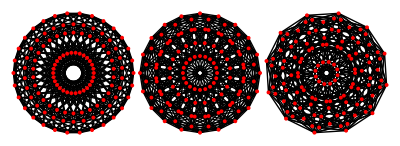

```mathematica
GraphicsRow[GraphData["SixHundredCellGraph","Images"]/.AbsolutePointSize[_]:>PointSize[.007],Spacings->-50,ImageSize->400]
```

### Scraping

Embeddings from http://en.wikipedia.org/wiki/600-cell

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

NautyTools Beta 0.2.0 by Mike Pilat, modified by Eric Weisstein

Based on NAUTY 2.2 by Brendan McKay

```mathematica
SVGToGraph[svg_,Method->"Wikipedia"]:=Module[{
v=Cases[svg,XMLElement["circle",x__,{}]:>ToExpression[{"cx","cy"}/.x],{1,Infinity}],e=Cases[svg,XMLElement["line",x__,{}]:>ToExpression[{{"x1","y1"},{"x2","y2"}}/.x],{1,Infinity}],
mult=10^2
},
Combinatorica`Graph[List/@(Round[mult e]/mult/.Thread[Round[mult v]/mult->Range[Length[v]]]),List/@v]
]
```

```mathematica
(g1=SVGToGraph[Import["http://upload.wikimedia.org/wikipedia/commons/f/f4/600-cell_graph_H4.svg","XML"],Method->"Wikipedia"])//RecognizeGraph
```

Reading CanonicalForms (first time only)...

Getting index for CanonicalForm (first time only)...

SixHundredCellGraph

```mathematica
(g2=SVGToGraph[Import["http://upload.wikimedia.org/wikipedia/commons/f/f8/600-cell_t0_p20.svg","XML"],Method->"Wikipedia"])//RecognizeGraph
```

SixHundredCellGraph

```mathematica
(g3=SVGToGraph[Import["http://upload.wikimedia.org/wikipedia/commons/f/fd/600-cell_t0_F4.svg","XML"],Method->"Wikipedia"])//RecognizeGraph
```

SixHundredCellGraph

```mathematica
ToCommonEdges[#,Combinatorica`Graph["SixHundredCellGraph"]]&/@{g1,g2,g3}/500
```

{{{1.40122,1.23682},{1.0939,1.20451},{1.00337,0.343222},{0.696042,0.31092},{1.52691,0.64549},{0.72232,0.560924},{1.37495,0.986812},{0.570352,0.902246},{1.32354,0.497732},{1.17158,0.15641},{0.92569,1.39133},{0.773724,1.05},{1.40122,0.736808},{0.59663,0.652242},{1.24926,0.395486},{0.444662,0.31092},{1.15534,1.28908},{0.350742,1.20451},{1.00337,0.947758},{0.198776,0.863192},{1.32354,1.10227},{0.826276,1.05},{0.92569,0.208674},{0.428422,0.15641},{1.17158,1.44359},{0.67431,1.39133},{0.773724,0.549996},{0.276456,0.497732},{1.27553,0.64549},{0.968206,0.613188},{1.02965,0.093218},{0.72232,0.060916},{0.87768,1.53908},{0.570352,1.50678},{0.631794,0.986812},{0.324466,0.95451},{0.903958,1.28908},{0.59663,1.25678},{0.506104,0.395486},{0.198776,0.363184},{1.02965,0.697754},{0.225052,0.613188},{0.87768,1.03908},{0.073086,0.95451},{0.826276,0.549996},{0.67431,0.208674},{0.428422,1.44359},{0.276456,1.10227},{1.27553,0.95451},{0.87768,0.060916},{1.47891,1.10227},{0.67431,1.0177},{1.23302,0.549996},{0.428422,0.46543},{1.02965,1.50678},{0.631794,0.613188},{1.40122,0.363184},{0.903958,0.31092},{1.00337,1.25678},{0.506104,1.20451},{0.968206,0.986812},{0.570352,0.093218},{1.17158,1.13457},{0.366982,1.05},{0.92569,0.582298},{0.121094,0.497732},{0.72232,1.53908},{0.324466,0.64549},{1.0939,0.395486},{0.59663,0.343222},{0.696042,1.28908},{0.198776,1.23682},{1.47891,0.497732},{1.17158,0.46543},{1.52691,0.95451},{1.02965,0.902246},{1.37495,0.613188},{0.87768,0.560924},{1.23302,1.05},{0.92569,1.0177},{1.40122,0.863192},{1.15534,0.31092},{1.24926,1.20451},{1.00337,0.652242},{0.67431,0.582298},{0.366982,0.549996},{0.72232,1.03908},{0.225052,0.986812},{0.570352,0.697754},{0.073086,0.64549},{0.428422,1.13457},{0.121094,1.10227},{0.59663,0.947758},{0.350742,0.395486},{0.444662,1.28908},{0.198776,0.736808},{1.29727,0.747736},{1.04589,0.247728},{1.04589,1.35227},{1.29727,0.852264},{0.302732,0.747736},{0.554112,0.247728},{0.554112,1.35227},{0.302732,0.852264},{1.54315,0.8},{1.04589,0.747736},{1.29727,0.247728},{0.8,0.195464},{1.29727,1.35227},{0.8,1.30001},{1.05138,0.8},{0.554112,0.747736},{1.04589,0.852264},{0.54862,0.8},{0.8,0.299994},{0.302732,0.247728},{0.8,1.40454},{0.302732,1.35227},{0.554112,0.852264},{0.056846,0.8}},{{1.57377,0.8},{1.5359,1.03911},{0.450986,0.977832},{0.413116,1.21694},{1.00905,0.867926},{0.909906,1.49392},{1.07698,0.523022},{0.977832,1.14901},{1.11896,1.42599},{0.690094,1.49392},{1.29679,0.523022},{0.867926,0.590946},{1.00905,0.732074},{0.909906,1.35807},{0.580188,0.8},{0.481042,1.42599},{1.11896,0.174008},{1.01981,0.8},{0.690094,0.241934},{0.590946,0.867926},{1.35807,0.690094},{1.29679,1.07698},{0.235284,0.867926},{0.174008,1.25481},{1.42599,0.34519},{1.36472,0.732074},{0.30321,0.523022},{0.241934,0.909906},{1.07698,1.07698},{1.03911,1.31609},{0.383062,1.18688},{0.34519,1.42599},{1.25481,0.174008},{1.21694,0.413116},{0.560892,0.283914},{0.523022,0.523022},{1.18688,0.383062},{1.14901,0.622168},{0.064102,0.560892},{0.026232,0.8},{0.622168,0.450986},{0.523022,1.07698},{0.690094,0.106082},{0.590946,0.732074},{0.732074,1.00905},{0.30321,1.07698},{0.909906,0.106082},{0.481042,0.174008},{1.42599,1.11896},{0.30321,1.29679},{1.31609,0.560892},{1.21694,1.18688},{0.622168,0.670798},{0.523022,1.29679},{1.5359,0.560892},{0.413116,0.738724},{0.861276,1.18688},{0.8,1.57377},{1.03911,0.283914},{0.977832,0.670798},{1.18688,0.861276},{0.064102,1.03911},{1.07698,0.30321},{0.977832,0.929202},{0.383062,0.413116},{0.283914,1.03911},{1.29679,0.30321},{0.174008,0.481042},{0.622168,0.929202},{0.560892,1.31609},{0.8,0.026232},{0.738724,0.413116},{1.07698,1.29679},{1.03911,1.5359},{1.35807,0.909906},{1.29679,1.29679},{0.929202,0.977832},{0.867926,1.36472},{1.18688,0.738724},{1.14901,0.977832},{1.42599,1.25481},{0.732074,1.36472},{1.49392,0.909906},{0.8,1.01981},{0.450986,0.622168},{0.413116,0.861276},{0.732074,0.235284},{0.670798,0.622168},{0.30321,0.30321},{0.241934,0.690094},{0.560892,0.064102},{0.523022,0.30321},{0.8,0.580188},{0.106082,0.690094},{0.867926,0.235284},{0.174008,0.34519},{1.18688,1.21694},{0.690094,1.35807},{1.49392,0.690094},{0.861276,0.413116},{0.738724,1.18688},{0.106082,0.909906},{0.909906,0.241934},{0.413116,0.383062},{1.31609,1.03911},{1.25481,1.42599},{0.622168,1.14901},{0.560892,1.5359},{1.42599,0.481042},{1.36472,0.867926},{0.732074,0.590946},{0.670798,0.977832},{0.929202,0.622168},{0.867926,1.00905},{0.235284,0.732074},{0.174008,1.11896},{1.03911,0.064102},{0.977832,0.450986},{0.34519,0.174008},{0.283914,0.560892}},{{1.42534,1.05569},{1.42534,0.839556},{0.652378,0.282726},{0.652378,0.066592},{0.930792,0.844066},{0.930792,0.278216},{1.14693,0.844066},{1.14693,0.278216},{0.903558,0.708764},{0.608312,0.413518},{1.46941,0.708764},{1.17416,0.413518},{0.772766,1.23055},{0.772766,0.664698},{0.47752,0.935302},{0.47752,0.369452},{1.12248,1.23055},{1.12248,0.664698},{0.827234,0.935302},{0.827234,0.369452},{1.07841,1.36134},{1.07841,1.01162},{0.30545,0.588376},{0.30545,0.238662},{1.29455,1.36134},{1.29455,1.01162},{0.521586,0.588376},{0.521586,0.238662},{0.755934,1.14693},{0.755934,0.930792},{0.278216,0.669208},{0.278216,0.453074},{1.32178,1.14693},{1.32178,0.930792},{0.844066,0.669208},{0.844066,0.453074},{0.947622,1.53341},{0.947622,1.31727},{0.17466,0.760444},{0.17466,0.54431},{0.453074,1.32178},{0.453074,0.755934},{0.669208,1.32178},{0.669208,0.755934},{0.42584,1.18648},{0.130594,0.891236},{0.991688,1.18648},{0.696442,0.891236},{1.15925,1.03886},{0.386284,0.265896},{1.18648,1.17416},{1.18648,0.608312},{0.708764,0.696442},{0.708764,0.130594},{1.50896,1.03886},{0.735998,0.265896},{0.664698,0.827234},{0.664698,0.47752},{1.23055,0.827234},{1.23055,0.47752},{0.864002,1.3341},{0.091038,0.561142},{0.891236,1.46941},{0.891236,0.903558},{0.413518,0.991688},{0.413518,0.42584},{1.21372,1.3341},{0.440752,0.561142},{0.369452,1.12248},{0.369452,0.772766},{0.935302,1.12248},{0.935302,0.772766},{1.01162,0.521586},{1.01162,0.30545},{1.3341,0.735998},{1.3341,0.386284},{1.03886,0.440752},{1.03886,0.091038},{1.36134,0.521586},{1.36134,0.30545},{1.31727,0.652378},{0.839556,0.17466},{1.53341,0.652378},{1.05569,0.17466},{0.238662,1.29455},{0.238662,1.07841},{0.561142,1.50896},{0.561142,1.15925},{0.265896,1.21372},{0.265896,0.864002},{0.588376,1.29455},{0.588376,1.07841},{0.54431,1.42534},{0.066592,0.947622},{0.760444,1.42534},{0.282726,0.947622},{1.27772,0.322282},{0.450286,0.8},{1.27772,1.27772},{0.8,1.14971},{0.8,0.450286},{0.322282,0.322282},{1.14971,0.8},{0.322282,1.27772},{1.10286,0.974856},{1.10286,0.625144},{0.625144,0.49714},{0.625144,0.147426},{1.45257,0.974856},{1.45257,0.625144},{0.974856,0.49714},{0.974856,0.147426},{0.625144,1.45257},{0.625144,1.10286},{0.147426,0.974856},{0.147426,0.625144},{0.974856,1.45257},{0.974856,1.10286},{0.49714,0.974856},{0.49714,0.625144}}}

```mathematica
GetGraphData["HundredTwentyCellGraph","File",#]&/@{"8.0","8.1"}
```

Reading 8.0 file database (first time only)...

Reading 8.1 file database (first time only)...

{29,30}

### Misc

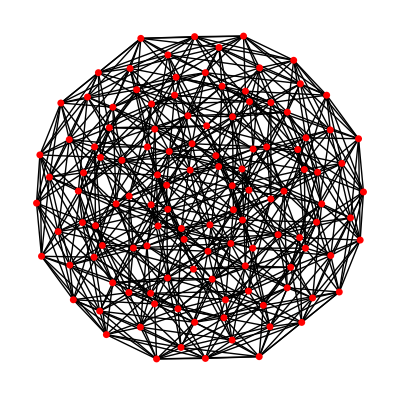

```mathematica
GraphData["600CellGraph","Image2D"]
```

```mathematica
GraphData["600CellGraph","Image3D"]
```

-Graphics3D-

### Van Oss Projection

The often published version is the Van Oss Projection of the 600-cell that dates to 1901, and which was used as the frontispiece to Regular Polytopes.   It's the Pi/15 shadow of a 3D 600-cell model.                                            
                                                                                                              
http://homepages.wmich.edu/~drichter/vanoss.htm                                                               
http://www.ams.org/notices/200101/fea-stillwell.pdf   (p. 22)                                                 
http://en.wikipedia.org/wiki/Image:600-cell_petrie_polygon.svg                                                
http://www.math.lsa.umich.edu/~jrs/coxplane2.html                                                             
http://mathworld.wolfram.com/600-Cell.html

```mathematica
{a,b,c,d} = {12,25,30,37};  (*radius of a ring of nodes*)
```

```mathematica
cell600 ={
{{a,a},{2,8}},{{a,a},{2,18}},{{a,a},{2,24}},{{a,b},{2,7}},{{a,b},{2,13}},{{a,b},{2,51}},{{a,b},{2,57}},{{a,c},{4,1}},{{a,c},{4,7}},{{b,b},{1,7}},{{b,c},{1,3}},{{b,c},{1,9}},{{b,c},{1,53}},{{b,c},{1,59}},{{b,d},{1,4}},{{b,d},{1,58}},{{c,c},{1,7}},{{c,d},{1,2}},{{c,d},{1,6}},{{c,d},{1,56}},{{c,d},{1,60}},{{d,d},{2,4}},{{d,d},{2,6}},{{d,d},{2,8}}};
```

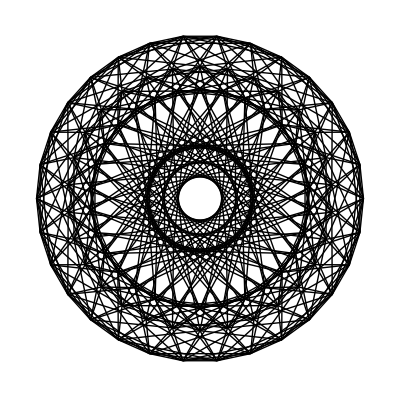

```mathematica
With[{lines =Transpose/@Flatten[Table[Mod[cell600+Table[{{0,0},{n,n}},{24}],60,1],{n,2,60,2}],1]},Graphics[Table[Line[#[[1]]{Cos[Pi #[[2]]/30],Sin[Pi#[[2]]/30]}&/@lines[[k]]],{k,1,720}]]]
```

```mathematica
FastIsomorphicQ[Graph["SixHundredCellGraph"],g=LinesToGraph[%,1]]
```

True

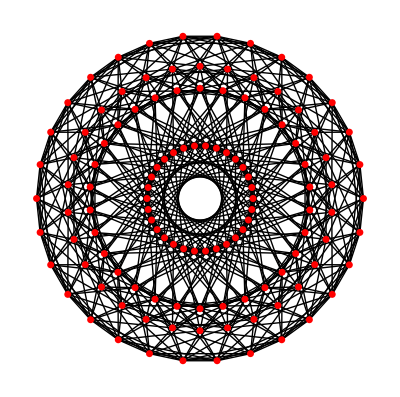

```mathematica
GraphPlot[g,Method->None]
```

```mathematica
ToCommonEdges[g,Graph["600CellGraph"]]
```

{{-0.0037,0},{-0.00361915,-0.000769273},{0.00216506,-0.00125},{0.00222943,-0.00200739},{-0.000802957,0.000891774},{-0.0006,-0.00103923},{-0.000802957,-0.000891774},{-0.000623735,-0.00293444},{-0.00185786,0.00167283},{0.00037082,0.00114127},{-0.00185,-0.00320429},{0.000386755,-0.00367973},{-0.00122021,0.00274064},{-0.00097082,0.000705342},{0.00101684,0.00228386},{0.00117378,0.000249494},{-0.00117378,-0.000249494},{-0.00101684,-0.00228386},{0.00097082,-0.000705342},{0.00122021,-0.00274064},{-0.00299336,0.00217481},{-0.00285317,0.000927051},{0.00285317,0.000927051},{0.00298357,-0.000313585},{-0.00298357,0.000313585},{-0.00285317,-0.000927051},{0.00285317,-0.000927051},{0.00299336,-0.00217481},{-0.00185,0.00320429},{-0.00176336,0.00242705},{0.00176336,0.00242705},{0.00185786,0.00167283},{-0.00185786,-0.00167283},{-0.00176336,-0.00242705},{0.00176336,-0.00242705},{0.00185,-0.00320429},{-0.00222943,0.00200739},{-0.00216506,0.00125},{0.00361915,0.000769273},{0.0037,0},{0.000623735,0.00293444},{0.000802957,0.000891774},{0.0006,0.00103923},{0.000802957,-0.000891774},{-0.000386755,0.00367973},{0.00185,0.00320429},{-0.00037082,-0.00114127},{0.00185786,-0.00167283},{-0.00338012,0.00150493},{0.0024863,0.000261321},{-0.00237764,0.000772542},{-0.00216506,-0.00125},{0.0012,0},{0.00146946,-0.00202254},{-0.00338012,-0.00150493},{0.00247578,-0.00274964},{-0.000519779,0.00244537},{-0.00037082,0.00114127},{-0.000519779,-0.00244537},{-0.000386755,-0.00367973},{-0.00247578,0.00274964},{0.00338012,0.00150493},{-0.00146946,0.00202254},{-0.0012,0},{0.00216506,0.00125},{0.00237764,-0.000772542},{-0.0024863,-0.000261321},{0.00338012,-0.00150493},{0.000386755,0.00367973},{0.000519779,0.00244537},{0.00037082,-0.00114127},{0.000519779,-0.00244537},{-0.00117378,0.000249494},{-0.00109625,-0.000488084},{-0.00237764,-0.000772542},{-0.00222943,-0.00200739},{-0.000125434,-0.00119343},{0,-0.0025},{-0.00122021,-0.00274064},{-0.00114336,-0.00351891},{-0.00298357,-0.000313585},{0.0006,-0.00103923},{-0.00299336,-0.00217481},{0.000623735,-0.00293444},{0.00114336,0.00351891},{0.00122021,0.00274064},{0,0.0025},{0.000125434,0.00119343},{0.00222943,0.00200739},{0.00237764,0.000772542},{0.00109625,0.000488084},{0.00117378,-0.000249494},{-0.000623735,0.00293444},{0.00299336,0.00217481},{-0.0006,0.00103923},{0.00298357,0.000313585},{-0.00146946,-0.00202254},{0,0.003},{-0.00361915,0.000769273},{-0.000125434,0.00119343},{0.000125434,-0.00119343},{0.00361915,-0.000769273},{0,-0.003},{0.00146946,0.00202254},{-0.00259808,0.0015},{-0.0024863,0.000261321},{0.00097082,0.000705342},{0.00109625,-0.000488084},{-0.00259808,-0.0015},{-0.00247578,-0.00274964},{0.00101684,-0.00228386},{0.00114336,-0.00351891},{-0.00114336,0.00351891},{-0.00101684,0.00228386},{0.00247578,0.00274964},{0.00259808,0.0015},{-0.00109625,0.000488084},{-0.00097082,-0.000705342},{0.0024863,-0.000261321},{0.00259808,-0.0015}}

```mathematica
GetGraphData["SixHundredCellGraph","File"]
```

24

### Shadow Cast of the 600 Cell

by Ed Pegg Jr
based on Coxeter's Regular Polytopes
based on Russell Towle's Regular Polytopes program:  http://library.wolfram.com/infocenter/MathSource/593/.

First, set up all the vertices.  When complete, vii335 will contain the 120 4-D vertices.

```mathematica
{a,b,c,d}=Table[Root[1-15 #1^2+60 #1^4-90 #1^6+45 #1^8&,n],{n,8,5,-1}];
CC[k_]:=RootReduce[ToRadicals[Cos[k Pi/30]]];
SS[k_]:=RootReduce[ToRadicals[Sin[k Pi/30]]];
```

```mathematica
vii335=
Flatten[Map[RootReduce[Simplify[#]]&,Table[
{{a CC[2 (-1+k)],a SS[2 (-1+k)],d CC[22 (-1+k)],d SS[22 (-1+k)]},{b CC[-1+2 k],b SS[-1+2 k],c CC[-11+22 k],c SS[-11+22 k]},{c CC[-1+2 k],c SS[-1+2 k],-b CC[-11+22 k],-b SS[-11+22 k]},{d CC[2 (-1+k)],d SS[2 (-1+k)],-a CC[22 (-1+k)],-a SS[22 (-1+k)]}},
{k,1,30}],{2}],1];
```

All are at distance 1 from the origin.

```mathematica
Union[N[Norm/@vii335]]
```

{1.}

Some rounding hackery to calculate the 720 edges.  With these, we can get a 2-D projection.

```mathematica
edges=Union[Sort/@Position[Round[100000Table[
N[Norm[vii335[[a]]-vii335[[b]]]],{a,1,120},{b,1,120}]],61803]];
```

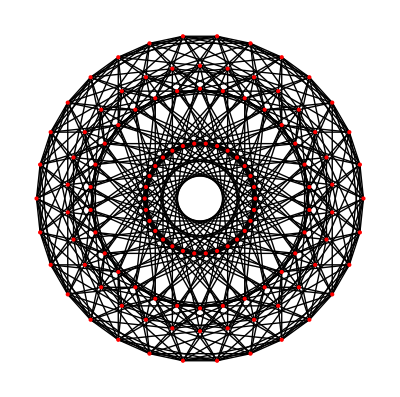

```mathematica
Graphics[{Line/@Map[Take[vii335[[#]],2]&,edges,{2}],Red,AbsolutePointSize[3],Point[Take[#,2]]&/@vii335}]
```

Here's the shadow projection again, this time in 3D.

```mathematica
Graphics3D[{Line/@Map[Take[vii335[[#]],3]&,edges,{2}],Red,AbsolutePointSize[5],Point[Take[#,3]]&/@vii335},Boxed-> False,SphericalRegion-> True,ViewPoint-> {0,0,60},ViewAngle->1°]
```

-Graphics3D-

### quaternion 120 group

Quaternion multiplication can be checked.

```mathematica
Cell600 =Module[{a,b,c,d,e,f,g,h,i},{{e,c,c,c},{a,c,c,c},{b,c,f,g},{b,c,f,h},{b,c,i,g},{b,c,i,h},{b,g,c,f},{b,g,c,i},{b,h,c,f},{b,h,c,i},{b,f,g,c},{b,f,h,c},{b,i,g,c},{b,i,h,c},{b,b,b,b},{b,b,b,d},{b,b,d,b},{b,b,d,d},{b,d,b,b},{b,d,b,d},{b,d,d,b},{b,d,d,d},{c,b,g,f},{c,b,g,i},{c,b,h,f},{c,b,h,i},{c,d,g,f},{c,d,g,i},{c,d,h,f},{c,d,h,i},{c,g,f,b},{c,g,f,d},{c,g,i,b},{c,g,i,d},{c,h,f,b},{c,h,f,d},{c,h,i,b},{c,h,i,d},{c,f,b,g},{c,f,b,h},{c,f,d,g},{c,f,d,h},{c,i,b,g},{c,i,b,h},{c,i,d,g},{c,i,d,h},{c,a,c,c},{c,c,a,c},{c,c,c,a},{c,c,c,e},{c,c,e,c},{c,e,c,c},{h,b,f,c},{h,b,i,c},{h,c,b,f},{h,c,b,i},{h,c,d,f},{h,c,d,i},{h,d,f,c},{h,d,i,c},{h,f,c,b},{h,f,c,d},{h,i,c,b},{h,i,c,d},{f,b,c,g},{f,b,c,h},{f,c,g,b},{f,c,g,d},{f,c,h,b},{f,c,h,d},{f,d,c,g},{f,d,c,h},{f,g,b,c},{f,g,d,c},{f,h,b,c},{f,h,d,c},{d,c,f,g},{d,c,f,h},{d,c,i,g},{d,c,i,h},{d,g,c,f},{d,g,c,i},{d,h,c,f},{d,h,c,i},{d,f,g,c},{d,f,h,c},{d,i,g,c},{d,i,h,c},{d,b,b,b},{d,b,b,d},{d,b,d,b},{d,b,d,d},{d,d,b,b},{d,d,b,d},{d,d,d,b},{d,d,d,d},{g,b,f,c},{g,b,i,c},{g,c,b,f},{g,c,b,i},{g,c,d,f},{g,c,d,i},{g,d,f,c},{g,d,i,c},{g,f,c,b},{g,f,c,d},{g,i,c,b},{g,i,c,d},{i,b,c,g},{i,b,c,h},{i,c,g,b},{i,c,g,d},{i,c,h,b},{i,c,h,d},{i,d,c,g},{i,d,c,h},{i,g,b,c},{i,g,d,c},{i,h,b,c},{i,h,d,c}}/.{a->-1,b->-1/2,c->0,d->1/2,e->1,f->1/4 (-1-√5),g->1/4 (1-√5),h->1/4 (-1+√5),i->1/4 (1+√5)}];
```

```mathematica
mult[{a1_,b1_,c1_,d1_},{a2_,b2_,c2_,d2_}]:=RootReduce[{a1 a2−b1 b2−c1 c2−d1 d2,a1 b2+b1 a2+c1 d2−d1 c2,a1 c2−b1 d2+c1 a2+d1 b2,a1 d2+b1 c2−c1 b2+d1 a2}];
```

```mathematica
quat120group =1+Reverse[-Graphics-[[1,1]]];
```

```mathematica
Take[quat120group,3] ==  Table[Position[Cell600,mult[Cell600[[m]],Cell600[[n]]]][[1,1]],{n,1,3},{m,1,120}]
```

True

### Manipulate

```mathematica
Manipulate[
With[{cell600 = {
{{a,a},{2,8}},{{a,a},{2,18}},{{a,a},{2,24}},{{a,b},{2,7}},{{a,b},{2,13}},{{a,b},{2,51}},{{a,b},{2,57}},{{a,c},{4,1}},{{a,c},{4,7}},{{b,b},{1,7}},{{b,c},{1,3}},{{b,c},{1,9}},{{b,c},{1,53}},{{b,c},{1,59}},{{b,d},{1,4}},{{b,d},{1,58}},{{c,c},{1,7}},{{c,d},{1,2}},{{c,d},{1,6}},{{c,d},{1,56}},{{c,d},{1,60}},{{d,d},{2,4}},{{d,d},{2,6}},{{d,d},{2,8}}}},
With[{lines =Transpose/@Flatten[Table[Mod[cell600+Table[{{0,0},{n,n}},{24}],60,1],{n,2,60,2}],1]},Graphics[Table[Line[#[[1]]{Cos[Pi #[[2]]/30],Sin[Pi#[[2]]/30]}&/@lines[[k]]],{k,1,720}]]]],
{{a,12},1,60},{{b,25},1,60},{{c,30},1,60},{{d,37},1,60}]
```

## Properties

### AutomorphismCount

```mathematica
GraphData["600CellGraph","AutomorphismCount"]
```

14400

### CyclePolynomial

A167985

```mathematica
GraphData["600CellGraph","CyclePolynomial"]
```

Missing[NotAvailable,{{3,1200},{4,5400},{5,29520},{6,187200},{7,1310400},{8,9813600},{9,77193600},{10,630538632},{11,5307656400}}]

### PathPolynomial

```mathematica
GraphData["600CellGraph","PathPolynomial"]
```

Missing[NotAvailable,{{1,720},{2,7920},{3,83520},{4,861120},{5,8755920},{6,88135920}}]

### Spectrum

```mathematica
GraphData["600CellGraph","Spectrum"]//SpectrumForm//TraditionalForm
```

(3 (1-√5))^4 (-3)^16 (2 (1-√5))^9 (-2)^36 0^25 3^16 (2 (1+√5))^9 (3 (1+√5))^4 12^1

### Graph Distances

```mathematica
{First[#],Length[#]}&/@Split[Distances[Graph["600CellGraph"],1]]
```

{{0,1},{1,12},{2,32},{3,42},{4,32},{5,1}}

```mathematica
Last/@%
```

{1,12,32,42,32,1}

```mathematica
Union[N[Norm/@(Subtract@@@Subsets[Cell600,{2}]),20],
SameTest->(Abs[N[#1-#2,20]]<.0001&)]//Length//Timing
```

{1.80348 Second,8}

### LCF

```mathematica
"LCF"/.GetGraphData["600CellGraph","NotationRules"]
```

Missing[NotAvailable]

```mathematica
GetGraphData["600CellGraph","HamiltonianCycles"]
```

Missing[NotAvailable,{{95,47,118,64,38,61,114,86,93,87,63,13,69,46,115,62,23,50,108,82,107,15,31,98,57,10,32,58,6,16,70,14,42,101,18,52,76,74,97,78,84,77,7,5,100,51,21,37,113,45,30,49,2,22,106,81,9,29,105,73,75,109,33,11,79,59,103,34,26,67,25,99,1,55,83,110,60,112,8,80,12,111,35,56,4,28,66,24,54,20,72,36,68,40,116,94,85,41,65,119,43,19,27,53,3,102,39,89,96,120,48,71,17,117,91,92,44,88,90,104}}]

```mathematica
HamiltonianCycles[Graph["600CellGraph"],1]//Timing
```

$Aborted

```mathematica
Tally[Last/@(lcf=LCF[GraphData["600CellGraph","EdgeIndices"],hc=Table[FindHamiltonianCycle[Graph["600CellGraph"],"RandomSeed"->i],{i,1000}],All])]//Timing
```

{177.801,{{1,1000}}}

```mathematica
Tally[Last/@(lcf=LCF[GraphData["600CellGraph","EdgeIndices"],hc=Table[FindHamiltonianCycle[Graph["600CellGraph"],"RandomSeed"->i],{i,1001,10^4}],All])]//Timing
```

{1721.08,{{1,9000}}}

```mathematica
Tally[Last/@(lcf=LCF[GraphData["600CellGraph","EdgeIndices"],hc=Table[FindHamiltonianCycle[Graph["600CellGraph"],"RandomSeed"->i],{i,1+10^4,10^5}],All])]//Timing
```

{15291.7,{{1,89930}}}

## Minimum Vertex Coloring

```mathematica
coloring={1,2,3,1,4,1,1,2,1,5,2,1,1,3,3,2,2,3,3,1,2,1,5,5,5,5,1,2,4,2,4,1,1,4,2,4,1,3,2,1,2,1,1,4,1,2,5,1,3,2,3,4,2,4,3,5,2,4,5,5,5,3,4,2,4,3,2,3,5,5,4,2,3,2,2,3,5,5,3,4,4,4,5,2,4,3,5,5,3,2,2,3,2,5,4,4,1,3,4,5,5,4,3,1,5,5,1,3,4,1,4,3,3,4,1,4,3,1,5,5};
```

```mathematica
ColoringQ[Graph["SixHundredCellGraph"],coloring]
```

True

```mathematica
SetProperty[GraphData["SixHundredCellGraph"],System`VertexStyle->MapIndexed[#2[[1]]->{Red,Orange,Yellow,Green,Blue}[[#]]&,coloring]]
```

-Graphics-

## Projection

```mathematica
spc={{1,2,3},{1,2,4},{1,3,4},{2,3,4}};
```

```mathematica
d=Union[ Map[N[Norm[First@Cell600-#]]&, Rest@Cell600],
SameTest->(Chop[#1-#2]==0&)];
v = (rota4[#1, Pi*11/15, Pi/15] & ) /@ Cell600;
c=Table[
a=Drop[v,i-1];
{First@a,#}& /@ Select[Rest@a, N[Norm[First@a-#]]<N[d[[2]]]&],
{i,Length[v]}];
v1=Map[#[[ spc[[2]] ]]&, v];
g=Map[#[[ spc[[2]] ]]&, Flatten[c,1], {-2} ];
Show[Graphics3D[{Line /@ Union[g],PointSize[.02],Point/@v1} ],
Boxed->False,
ViewPoint->{0,0,200}];
```

```mathematica
gr=FromEdges[Cell600,c];
ShowGraph[gr]
```

⁃Graphics⁃

## Animation

```mathematica
FromEdges[v_List,e_List]:=Module[{i},
FromUnorderedPairs[Flatten[e,1]/.Thread[Table[v[[i]]->i,{i,Length[v]}]]]
]
```

```mathematica
(* Animation *)
(* r= which 3-space:1(w=0),2(z=0),3(y=0),4(x=0)*)
(* t= PlotRange*)

PolytopeMovie[vertices_List,ang_List:{0,Pi,Pi/30},r_:1,t_:2,opts___]:=Module[{v,d,c,a,v1,g},
Table[v=(rota4[#1,i,i]&)/@vertices;
d=Union[(N[mag[v[[1]]-#1]]&)/@Rest[v],SameTest->(Chop[#1-#2]==0&)];
c=Table[a=Drop[v,i-1]; ({First[a],#1}&)/@Select[Rest[a],Chop[N[mag[First[a]-#1]]-d[[1]]]==0&],{i,Length[v]}];
v1=(#1[[spc[[r]]]]&)/@v;
g=Map[#1[[spc[[r]]]]&,Flatten[c,1],{-2}];
Show[Graphics3D[{Line/@Union[g],PointSize[0.02],Point/@v1}],Boxed->False,PlotRange->{{-t,t},{-t,t},{-t,t}},opts],{i,ang[[1]],ang[[2]]-ang[[3]],ang[[3]]}]
]
```

```mathematica
movie=PolytopeMovie[v335,{0,Pi/2,Pi/30},1,2,ViewPoint->{0,-1,2}];
```

```mathematica
WriteLiveAnimationForm["cell600.m",movie,AnimationDirection->ForwardBackward]
```

```mathematica
Export[gifs<>"cell600.gif",movie,
"GIF",ImageSize->200,AnimationDirection->ForwardBackward]
```

Phosphine:MathOztex:gifs:600cell.gif